# Байдук Я.А.

## Лабораторная работа №1 : Списки. Строки и текст

## 1.1

### 1. Используя функцию Range создайте список {1,2,3,4}

```mathematica
Range[4](* Создаёт список {1,2,3,4} *)
```

{1,2,3,4}

### 2. Создайте список из натуральных чисел от 1 до 100

```mathematica
Range[100](* Создаёт список из натуральных чисел от 1 до 100 *)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

### 3. Используя функции Range и Reverse, создайте список {4,3,2,1}

```mathematica
Reverse[Range[4]](* Создаёт список {4,3,2,1} *)
```

{4,3,2,1}

### 4. Создайте список из натуральных чисел от 1 до 50 в обратном порядке

```mathematica
Reverse[Range[50]](* Создаёт список {50,49,...2,1} *)
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
5.Используя функции Range,Reverse и Join,создайте список {1,2,3,4,4,3,2,1}
```

```mathematica
Join[Range[4],Reverse[Range[4]]](* Создаёт список {1,2,3,4,4,3,2,1} *)
```

```mathematica
6. Нарисовать график списка чисел,которые возрастают от 1 до 100,а затем убывают от 100
до 1
```

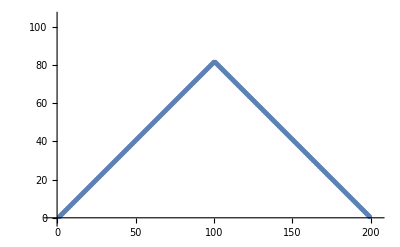

```mathematica
ListPlot[Join[Range[100],Reverse[Range[100]]]](* Рисует график от 1 до 100 на возр и от 100 до 1 на убыв *)
```

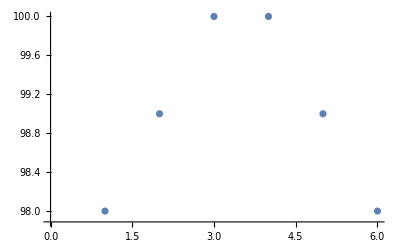

```mathematica
ListPlot[{98,99,100,100,99,98}]
```

```mathematica
Join[Range[100],Reverse[Range[100]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,100,99,98,97,96,95,94,93,92,91,90,89,88,87,86,85,84,83,82,81,80,79,78,77,76,75,74,73,72,71,70,69,68,67,66,65,64,63,62,61,60,59,58,57,56,55,54,53,52,51,50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
7. Используя функции Range и RandomInteger создайте список случайно генерированной
длины,не превышающей число 10
```

```mathematica
Range[RandomInteger[10]](* Создаёт список случайно генерированной длины *)
```

{1,2,3,4,5,6,7}

```mathematica
8.  Найти простейшую форму для команды Reverse[Reverse[Range[10]]]
```

```mathematica
Range[10](* Простейшая форма команды Reverse[Reverse[Range[10]]] *)
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
9. Найти простейшую форму для команды Join[{1,2},Join[{3,4},{5}]]
```

```mathematica
Range[5](* Простейшая форма команды Join[{1,2},Join[{3,4},{5}]] *)
```

{1,2,3,4,5}

```mathematica
10. Найти простейшую форму для команды Join[Range[10],Join[Range[10],Range[5]]]
```

```mathematica
Join[Range[10],Range[10],Range[5]](* Простейшая форма команды Join[Range[10],Join[Range[10],Range[5]]] *)
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

```mathematica
11.Найти простейшую форму для команды Reverse[Join[Range[20],Reverse[Range[20]]]]
```

```mathematica
Join[Range[20],Reverse[Range[20]]](* Простейшая форма команды Reverse[Join[Range[20],Reverse[Range[20]]]] *)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

## 1.2 Строки и текст (Strings and Text)

### 1. Присоедините две копии строки «Здравствуйте».

```mathematica
StringJoin["Здравствуйте","Здравствуйте"](*Соединяет две строки*)
```

ЗдравствуйтеЗдравствуйте

### 2. Создайте единую строку всего английского алфавита заглавными буквами

```mathematica
ToUpperCase[Alphabet[]](*Переводит алфавит в верхний регистр*)
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

### 3. Сгенерируйте строку английского алфавита в обратном порядке

```mathematica
Reverse[Alphabet[]](*Показывает алфавит в обратном порядке*)
```

{z,y,x,w,v,u,t,s,r,q,p,o,n,m,l,k,j,i,h,g,f,e,d,c,b,a}

### 4. Объедините 100 копий строки «ABCD»

```mathematica
StringJoin[StringRepeat["ABCD",100]](*объединяет копии строк*)
```

ABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCD

### 5. Используйте StringTake, StringJoin и Alphabet, чтобы получить «abcdef»

```mathematica
StringTake[StringJoin[Alphabet[]],6](*объединяем алфавит в строку и берём часть*)
```

abcdef

### 6. Создайте столбец с числом элементов, равных длине строки «это о строках» и содержащих число букв (включая пробелы) равное номеру элемента

```mathematica
Column[Table[StringTake["это о строках", n], {n, StringLength["это о строках"]}]](*Создал столбец из букв строки "это о строках"*)
```

э
эт
это
это 
это о
это о 
это о с
это о ст
это о стр
это о стро
это о строк
это о строка
это о строках

### 7. Создайте гистограмму длин слов в «Давным-давно, в далекой галактике, далеко».

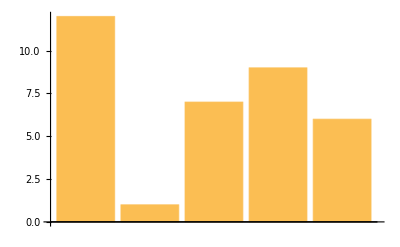

```mathematica
BarChart[StringLength[TextWords["Давным-давно, в далекой галактике, далеко"]]](*Создал гистрограмму длин слов строки «Давным-давно,в далекой галактике*)
```

### 8. Найдите максимальную длину слова среди английских слов из WordList []

```mathematica
Max[StringLength[WordList[]]](*Находит максимально длинное слово из перечисленных*)
```

```mathematica
21
```

### 9. Используйте Length, чтобы найти длину русского алфавита

```mathematica
Length[Alphabet["Russian"]](*Находит длину рус. алфавита*)
```

33

### 10. Создайте строку из заглавных букв греческого алфавита в обратном порядке.

```mathematica
ToUpperCase[StringJoin[Reverse[Alphabet["Greek"]]]](*Создал строку из заглавных букв греческого алфавита в обратном порядке*)
```

ΩΨΧΦΥΤΣΡΠΟΞΝΜΛΚΙΘΗΖΕΔΓΒΑ

## 1.3 Чистые функции

```mathematica
1. Используйте Range и чистую функцию для создания списка из квадратов первых 20
натуральных чисел
```

```mathematica
#^2&/@Range[20](*Чистая функция для создания списка квадратов первых 20 чисел*)
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
2. Составьте список из результатов смешивания желтого,зеленого и синего цветов с красным
цветом
```

```mathematica
Blend[{#,Red},1/2]&/@{Yellow,Green,Blue}(*Чистая функция для составления списка смешивания цветов*)
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
3. Создайте список столбцов в рамках,содержащих прописные и строчные версии каждой
буквы алфавита
```

```mathematica
Framed[Column[{ToUpperCase[#],#}]]&/@Alphabet[](*Создал список столбцов в рамках, сод. прописные версии каждой буквы алфавита*)
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
4. Составьте список букв алфавита в случайных цветах в рамках,имеющих случайные цвета
фона
```

```mathematica
Framed[Style[#,RandomColor[]], Background->RandomColor[]]&/@Alphabet[](*Составила список букв алфавита в случайных цветах в рамках,имеющих случайные цвета фона*)
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
5.Напишите в более простой форме команду (#^2+1&)/@Range[10]
```

```mathematica
Range[10]^2+1(*Упрощенная форма команды (#^2+1&)/@Range[10]*)
```

{2,5,10,17,26,37,50,65,82,101}

## 1.4 Композиции функций и их программирование

```mathematica
1. Составьте список результатов использования функции Blur до 10 раз начиная с
растрированного размера 30 “X” (Используйте:Rasterize[Style)
```

```mathematica
NestList[Blur,Rasterize[x,RasterSize->30],10](*Составил список результатов исп функции Blur до 10 раз с растрированного размера 30 "Х"*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
2. Начните с x,затем создайте список,использовав последовательно функцию Framed до 10
раз,используя каждый раз случайный цвет фона
```

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10](*Создал список, исп функцию Framed до 10 раз*)
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
3. Начните с размера 50 для “A”,затем создайте список вложенного применения Framed и случайного вращения 5 раз
```

```mathematica
NestList[Rotate[Framed[#],Pi*Random[]]&,Style["A",FontSize->50], 5](*Создал список вложенного применения Framed и случайного вращения 5 раз*)
```

{A,A,A,A,A,A}

```mathematica
4. Создайте линейный график из 100 итераций логического итерационного отображения 4 #(1-#)&,начиная с 0.2
```

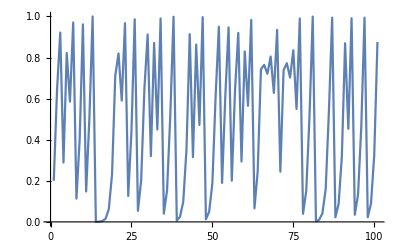

```mathematica
ListLinePlot[NestList[4 #(1-#)&,0.2,100]](*Создал линейный график из 100 итераций*)
```

```mathematica
5. Найдите числовое значение результата из 30 итераций применения функции 1+1/#&,начиная с 1
```

```mathematica
Nest[1+1/#&,1,30](*Нашёла числовое зн результата из 30 итераций функции 1+1/#&*)
```

2178309/1346269

```mathematica
6. Создайте список из первых 10 степеней 3 (начиная с 0) путем вложенного умножения
```

```mathematica
NestList[3*#&,1,10](*Создала список из первых 10 степеней 3*)
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

```mathematica
7. Составьте список результатов действия вложенной функции (метод Ньютона) (#+2/#)/2 до
5 раз,начиная с 1.0 ,  а затем вычтите 2 из всех результатов
```

```mathematica
NestList[(#+2/#)/2-Sqrt[2]&,1.0,5](*Составила список исп метод Ньютона для вложенной функции*)
```

{1.,0.0857864,10.2855,3.82578,0.76006,0.281502}

```mathematica
8. Создайте список из 5 степеней числа 2,т.е.2^2^2...^2 n раз,причем n меняется от 0 до 4
```

```mathematica
NestList[#^2&,Table[2,1],5](*Создала список из 5 степеней числа 2*)
```

{{2},{4},{16},{256},{65536},{4294967296}}

## 1.5 Определение функций пользователя

```mathematica
1. Определите функцию f,которая вычисляет квадрат ее аргумента
```

```mathematica
f[x_]:=x^2;(*Определила функцию кот вычисляет квадрат её аргумента*)
f[4]
```

16

```mathematica
2. Определите функцию poly,которая имеет целочисленное значение аргумента и создает
изображение оранжевого правильного многоугольника с числом сторон,равным значению
этого аргумента
```

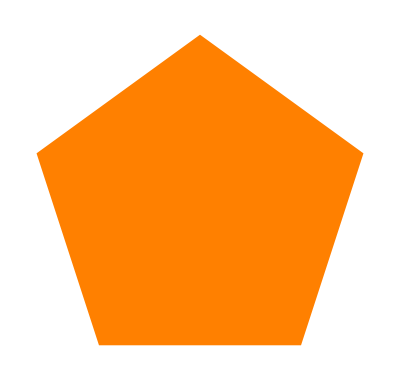

```mathematica
poly[x_]:=Graphics[{Orange,Polygon[CirclePoints[x]]}];(*Определила функцию poly, кот создаёт прав многоугольник с кол сторон == аргументу*)
poly[5]
```

```mathematica
3. Определите функцию f,которая берет список из двух элементов и помещает их в обратном
порядке
```

```mathematica
f[{x_,y_}]:=Reverse[{x,y}];(*Определил функцию, кот берёт список из 2-х элементов и выводит их в обратном порядке*)
f[{8,1}]
```

{1,8}

```mathematica
4. Определите функцию f,которая имеет два аргумента и дает результат в виде дроби,где
числитель равен произведению этих элементов,а знаменатель-их сумме
```

```mathematica
f[x_,y_]:= (x*y)/(x+y);(*Определил функцию, кот имеет 2 арг и даёт результат в виде дроби*)
f[3,4]
```

12/7

```mathematica
5. Определите функцию f,которая имеет два аргумента и дает результат в виде списка трех
элементов,которые соответственно равны сумме,разности и частному этих аргументов
```

```mathematica
f[x_,y_]:={x+y,x-y,x/y};(*Определил функцию, кот имеет 2 арг и даёт рез в виде списка 3 элементов*)
f[5,3]
```

{8,2,5/3}

```mathematica
6. Определите функцию evenodd,которая зависит от одного целочисленного аргумента и
имеет значение Black,если ее аргумент четный,значение-White в противном случае,значение
Red-если аргумент равен нулю.
```

```mathematica
evenodd[0]:=Red;
evenodd[x_]:= If[EvenQ[x], Black,White];(*Определил функцию, кот зависит от одного аргумента от которого зависит цвет*)
evenodd[0]
```

RGBColor[1, 0, 0]

```mathematica
7. Определите функцию Fibonacci f с f[0]=1 и f[1]=1,а f[n] для натурального числа n является
суммой f[n-1] и f[n-2]
```

```mathematica
f[0]:=1;
f[1]:=1;
f[x_]:=f[x-1]+f[x-2];(*Определил функцию Фибоначчи*)
f[4]
```

5